# Gradient Descent

Aaron Lopes

## Backstory

### Mathematical Motivation

```mathematica
Clear[g,x,y]
```

```mathematica
WordDefinition["gradient"]
```

{the property possessed by a line or surface that departs from the horizontal,a graded change in the magnitude of some physical quantity or dimension}

In mathematics, the term gradient holds several definitions. Most generally, it is interchangeable with slope, describing the rate of change of a function. In multivariate and vector calculus, it describes the direction in which the steepest upward rate of change occurs within a function. This can be found by taking the derivative of the function with respect to (w.r.t) its independent variables.

```mathematica
g[x,y] = (x/a)^2-(y/b)^2
```

x^2/a^2-y^2/b^2

```mathematica
Manipulate[Plot3D[g[x,y],{x,-5,5},{y,-5,5}],{a,1,10},{b,1,10}]
```

```mathematica
grad = Grad[g[x,y], {x,y}]
```

{2 x,-2 y}

If we plot the gradient as a vector field, we see that the x and y vectors correspond to the direction of steepest ascent.

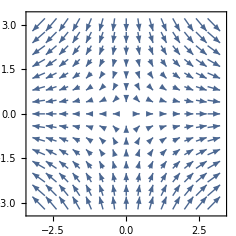

```mathematica
VectorPlot[grad, {x, -3, 3}, {y,-3,3}]
```

Conversely, the negative gradient represents the direction of steepest descent.

```mathematica
grad = -grad
```

{-2 x,2 y}

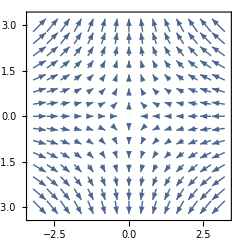

```mathematica
VectorPlot[(grad), {x,-3,3}, {y,-3,3}]
```

### Application to Machine Learning

The method of gradient descent as a minimizer for nonlinear functions was first introduced by mathematician Augustin-Louis Cauchy,

```mathematica
WebImageSearch["Augustin-Louis Cauchy"]
```

Dataset[<>]

## Working Example of Learning with Gradient Descent

```mathematica
ResourceObject["Infectious Diseases by Country 2009-2014"]
```

ResourceObject[…]